# Elevation Data

## Try-and-error with Geo commands

### Comparison with a different format

```mathematica
data=GeoElevationData[GeoDisk[Entity["Mountain","MountEverest"],Quantity[.05,"Miles"]]];
%//FullForm
```

StructuredArray[QuantityArray,List[4,5],StructuredArray`StructuredData[QuantityArray,List[List[28641.7,28684.4,28681.1,28638.5,28523.6],List[28618.8,28654.9,28628.6,28546.6,28428.5],List[28589.2,28599.1,28530.2,28435.,28333.3],List[28533.5,28549.9,28451.4,28333.3,28143.]],"Feet",List[List[1],List[2]]]]

```mathematica
ListPlot3D[Reverse[data],MeshFunctions->{#3&},Mesh->30]
```

-Graphics3D-

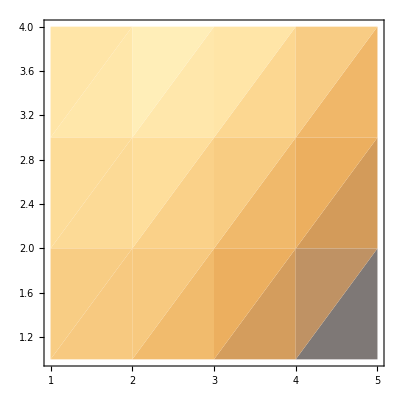

```mathematica
ListDensityPlot[Reverse[data]]
```